```mathematica
P[x_,α_,β_,μ_,σ_,m_,s_ ,n_]= (Abs[α-β]*x^(α-β-1)/(Sqrt[2*Pi*σ^2*n*s^2]))*Exp[-(x^(α-β)-μ*n*m)^2/(2*σ^2*n*s^2)]
```

(ⅇ^(-((x^(α-β)-m n μ)^2)/(2 n s^2 σ^2)) x^(-1+α-β) Abs[α-β])/(√(2 π) √(n s^2 σ^2))

```mathematica
α=1;
β=2;
n=10;
m=10;
s=.1;
μ = 10;
σ=.01;
```

General::munfl: Exp[-1.303×10^10] is too small to represent as a normalized machine number; precision may be lost.

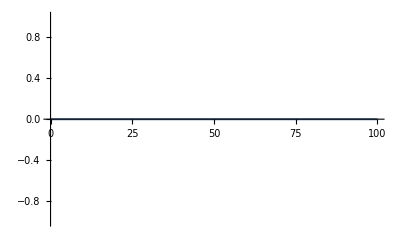

```mathematica
Plot[P[x,α,β,μ,σ,m,s,n],{x,0,100},PlotRange->All]
```

```mathematica
Solve[x^a+b*x^(3*a)==d,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(-(2/3)^(1/3)/((9 b^2 d+√3 √(4 b^3+27 b^4 d^2))^(1/3))+((9 b^2 d+√3 √(4 b^3+27 b^4 d^2))^(1/3))/(2^(1/3) 3^(2/3) b))^(1/a)},{x→((1+ⅈ √3)/(2^(2/3) 3^(1/3) (9 b^2 d+√3 √(4 b^3+27 b^4 d^2))^(1/3))-((1-ⅈ √3) (9 b^2 d+√3 √(4 b^3+27 b^4 d^2))^(1/3))/(2 2^(1/3) 3^(2/3) b))^(1/a)},{x→((1-ⅈ √3)/(2^(2/3) 3^(1/3) (9 b^2 d+√3 √(4 b^3+27 b^4 d^2))^(1/3))-((1+ⅈ √3) (9 b^2 d+√3 √(4 b^3+27 b^4 d^2))^(1/3))/(2 2^(1/3) 3^(2/3) b))^(1/a)}}